# Identities involving Spherical Bessel Functions

While integrating the internal electromagnetic fields inside a sphere, several integrals of products of spherical Bessel functions arise. These integrals are in turn proportional to the transition matrix elements between the internal and the scattered fields of the sphere. To the best of my knowledge, these relationships are not present in the literature. This may be due to the fact that the far field in Mie theory can simply be obtained by integrating the scattered field over a unit sphere via the following expression

F(k̂)=ika^2/(4π)∫k̂×(ŝ×E_sca(s)+η_0 k̂× ŝ× H_sca(s))ⅆ ŝ

This expression can be evaluated on any spherical surface of radius “a” that encloses the actual sphere. However, in the application of Mie theory relevant to my work in this project, I need to evaluate F via the following expression over the volume of the sphere,

F(k̂)=k^2/(4π)(n^2-1)∫_sphere (I-k̂ k̂)·E_sph(s)ⅆs

This expression leads to three integrals that must be evaluated in a general form to confirm that the internal field volume integral in the above expression yields exactly the same result as the surface integral. Of course, this is ensured by the surface equivalence theorem. However, my purpose here is to validate the numerical implementation of both ways of calculating the scattering matrix. For this, I find it reassuring to first learn how the expressions that follow from (1) will follow from (2). The details are outlined in my notes. Here  I only compute the two types of integrals arising in the analysis:

A_l(n,z)=∫_0^z x^2 j_l(x)j_l(nx)ⅆx
B_l(n,z)=(n^2-1)∫_0^z [ψ'(x)ψ'(nx)+l(l+1)j_l(x)j_l(nx)]ⅆx

## Definitions of elementary functions

First I define the Riccati functions and their derivatives so that the expressions above can be formed easily. I use the symbol ψ for the function x j_l(x) and the symbol ξ(x)=xh^(1)(x) where h^(1) is the spherical Hankel function of the first kind.

```mathematica
ψ[l_,z_] := z SphericalBesselJ[l,z]
ξ[l_,z_] := z SphericalHankelH1[l,z]
Dψ[l_,z_]:= Evaluate[D[ψ[l,z],z]]
Dξ[l_,z_]:= Evaluate[D[ξ[l,z],z]]

alpha1[l_,n_,z_]:= ψ[l,z] Dψ[l,n z]-1/n  Dψ[l,z] ψ[l,n z]
alpha2[l_,n_,z_]:= ψ[l,z] Dψ[l,n z]-n Dψ[l,z] ψ[l,n z]
beta1[l_,n_,z_]:= ξ[l,z] Dψ[l,n z]-1/n Dξ[l, z] ψ[l, n z]
beta2[l_,n_,z_]:= ξ[l,z] Dψ[l,n z]- n Dξ[l, z] ψ[l, n z]

TscaM[l_,n_,z_]:= -alpha1[l,n,z]/beta1[l,n,z]
TscaN[l_,n_,z_]:= -alpha2[l,n,z]/beta2[l,n,z]
```

### Integral A_l(n,z)

The first integral is over spherical Bessel functions. It has a closed form expression. The denominator going to zero as n -> 1 is a removable singularity as is confirmed below using the limit function.

```mathematica
A=Simplify[(1-n^2)Integrate[SphericalBesselJ[l,n x] SphericalBesselJ[l,x]  x^2,x,Assumptions->{l>1, l ∈ Integers,x∈ Reals}]];
TraditionalForm[A]
```

(π x^(3/2) (n l+1/2x l-1/2n x-l-1/2x l+1/2n x))/(2 √(n x))

The above expression is equivalent to the following, after I substitute the spherical Bessel function for the Bessel functions of half-integer order above:

```mathematica
RHS1[l_,n_,z_]:= n z^2 (SphericalBesselJ[l-1,n z] SphericalBesselJ[l,z]-1/n SphericalBesselJ[l-1,z] SphericalBesselJ[l,n z])
```

Verify that the result above is equal to α_(1l)(n,z)

```mathematica
FullSimplify[alpha1[l,n,z]-RHS1[l,n,z]]
```

0

```mathematica
A/.n->  2
```

(π x (-2 BesselJ[-1/2+l,2 x] BesselJ[1/2+l,x]+BesselJ[-1/2+l,x] BesselJ[1/2+l,2 x]))/(2 √2)

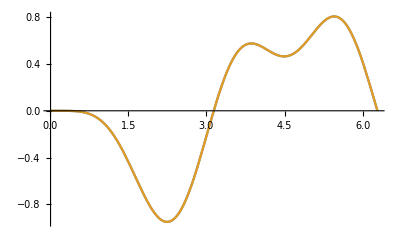

```mathematica
Plot[{alpha1[1,2,x],A/.{n-> 2,l-> 1}},{x,0.01,2π}]
```

### Integral B_l(n,z)

#### Taylor Series Expansion at z=0

This integral has no direct analytical expression available. I first check that the expressions

```mathematica
B[l_,n_,z_] := -(n^2-1)( Dψ[l,n z]Dψ[l,z] + l(l+1) SphericalBesselJ[l,n z]SphericalBesselJ[l,z])
```

```mathematica
lval=1;
maxterm=3;
temp1 = Series[B[lval,n,z],{z,0,maxterm},Assumptions->{z∈ Reals, z>0}];
temp1=FullSimplify[Integrate[Normal[temp1],z]];
temp2 = Series[alpha2[lval,n,z],{z,0,maxterm},Assumptions->{z∈ Reals, z>0}];
temp2= FullSimplify[Normal[temp2]];

Print["Taylor expansion:\nB_l(l,n,z) = ",TraditionalForm[temp1]]
Print["α_(2  l)(l,n,z) = ",TraditionalForm[temp2]]
FullSimplify[temp1-temp2]
```

Taylor expansion:
B_l(l,n,z) = -2/9 n (n^2-1) z^3

α_(2  l)(l,n,z) = -2/9 n (n^2-1) z^3

0

#### Numerical Integration of B_l(n,z)

Using numerical integration, I verify below that the integral B_l(n,z)=α_(2l)(n,z) for any arbitrary value of n, z, l. One can change the values of each of these parameters and find that the difference between numerically evaluated B_l(n,z) is equal to α_(2l)(n,z) within the numerical precision.

```mathematica
zval=3;
nval=2.0;
temp1 = Table[NIntegrate[B[l,nval,z],{z,0,zval}],{l,1,5}];
temp2 = Table[alpha2[l,nval,zval],{l,1,5}];
Print["α_(2  l)(n,z)         = ",temp2]
Print["B_l(n,z)          = ",temp1]
Print["B_l(n,z)-α_(2  l)(n,z) = ",temp1-temp2]
```

α_(2  l)(n,z)         = {-0.527632,-0.638098,-1.01051,-0.541271,-0.145354}

B_l(n,z)          = {-0.527632,-0.638098,-1.01051,-0.541271,-0.145354}

B_l(n,z)-α_(2  l)(n,z) = {-2.44249×10^-15,-3.44169×10^-15,-4.44089×10^-16,-1.33227×10^-15,-1.66533×10^-16}

```mathematica
alpha3[l_,n_,z_]:={ ψ[l,z],Dψ[l,n z], Dψ[l,z] ,ψ[l,n z]}
alpha3[1,2,3.]
alpha2[1,2,3.]
```

{1.03703,-0.111626,-0.204557,-1.00674}

-0.527632

## Spherical harmonics sums

```mathematica
l1=1
FullSimplify[Sum[SphericalHarmonicY[l1,m,θ,ϕ] SphericalHarmonicY[l,m,θ,γ],{m,-l1,l1}]]
```

1

1/4 ⅇ^(-ⅈ ϕ) √(3/π) (2 ⅇ^(ⅈ ϕ) Cos[θ] SphericalHarmonicY[l,0,θ,γ]+√2 Sin[θ] (SphericalHarmonicY[l,-1,θ,γ]-ⅇ^(2 ⅈ ϕ) SphericalHarmonicY[l,1,θ,γ]))

## Taylor Series of Scattering Coefficients

```mathematica
Series[TscaM[1,n,z],{z,0,3}]
Series[TscaN[1,n,z],{z,0,3}]
Series[TscaN[2,n,z],{z,0,3}]
```

O[z]^5

(2 ⅈ (-1+n^2) z^3)/(3 (2+n^2))+O[z]^4

O[z]^5